## Useful functions

```mathematica
<<MaTeX`
texStyle={FontFamily->"Latin Modern Roman",FontSize->12,Magnification->1.6};
ParallelEvaluate[Off[General::munfl,FindFit::cvmit]];
Off[General::munfl,General::stop,LinearSolve::luc,FindFit::cvmit]
SetDirectory[NotebookDirectory[]]
```

/home/kirscher/kette_repo/31_resonances/code

```mathematica
RiccatiBesselJ[z_,l_]:=z SphericalBesselJ[l,z];
RiccatiBesselN[z_,l_]:=(-1.)^l z SphericalBesselY[l,z];
```

```mathematica
(*Boundery conditions for the wavefunction*)
alpha[ra_,ka_,la_,ha_]:=RiccatiBesselN[ka (ra+ha),la]/RiccatiBesselN[ka ra,la]

beta[rb_,kb_,lb_,hb_]:=RiccatiBesselJ[kb (rb+hb),lb]-RiccatiBesselJ[kb rb,lb] (RiccatiBesselN[kb (rb+hb),lb]/RiccatiBesselN[kb rb,lb])
```

LEC=(Λ,a_(3-1)^(S-wave) [fm],C_(2-body) [MeV],C_(3-body) [MeV])
the triton-proton S-wave scattering length is used to calibrate the core parameter and
was obtained by R. Lazauskas.

```mathematica
(* Nuclear E2=2.22 E3=8.48 ℏc=198*)
(* λ a0,r0 (Martin, 23) a1,r1 (Martin,45) a0 (Rimas, unprojected, 6) a1 (Rimas, unprojected, 7) a0 (Rimas, projected, 8) a1 (Rimas, projected, 9)*)
a0a1NUCLmartinrimas=Import[NotebookDirectory[]<>"../data/a0-a1_nucl_Rimas-Martin.dat","Table"][[2;;]];
(* λ C0,D0 (Martin, 23) C0,D0 (Rimas, unprojected, 45) C0,Do (Rimas, projected, 67)*)
LECsNUCLmartinrimas=Import[NotebookDirectory[]<>"../data/LECs_nucl_Rimas-Martin.dat","Table"][[2;;]];
LECsUNITmartinrimas=Import[NotebookDirectory[]<>"../data/LECs_univ_Rimas-Martin.dat","Table"][[2;;]];

activeLEC=LECsUNITmartinrimas(*LECsNUCLmartinrimas[[All,{1,2,3}]]*);
```

(non)local resonating-group potentials from a 2- and 3-body contact interaction for TRIMER-FERMION (ABC-A)

W_(non-local) takes the Energy (e_) in [MeV]

```mathematica
NormTF[core_?ArrayQ]:=1./Sqrt[Total[Flatten[Table[core[[i]][[1]] core[[j]][[1]] (Pi/(core[[i]][[2]]+core[[j]][[2]]))^1.5,{i,Length[core]},{j,Length[core]}]]]];

VlocTF[r_,lam_,Cc_,Dd_,Aa_,Bb_]:=Block[{eta2,eta3,w2,w3},
eta2=2. Cc/(2. (Aa+Bb)(3. Aa+3. Bb+2. lam))^(3./2.);
w2=3. (Aa+Bb) lam/(3. (Aa+Bb)+2. lam);
eta3=Dd/(6. (Aa+Bb)^2+16. (Aa+Bb) lam+2. lam^2)^(3./2.);
w3=(3. (Aa+Bb) lam ((Aa+Bb)+2. lam)/(3. (Aa+Bb)^2+8. (Aa+Bb) lam+lam^2));
eta2 Exp[-w2 r^2]+eta3  Exp[-w3 r^2]
];

WnolocTF[r_,rp_,Ee_,lam_,Cc_,Dd_,Aa_,Bb_,Ll_,TwoMyOverHBsq_]:=Block[{zeta1,zeta2,zeta3,a1,b1,c1,a2,b2,c2,a3,b3,c3},
zeta1=(27./64.)(2 (Aa+Bb))^(-3./2.) (1./TwoMyOverHBsq);
a1=(Aa+9. Bb) 3./32.;
b1=(Aa+Bb) 9./16.;
c1=(9. Aa+Bb) 3./32.;

zeta2=-27./32. Cc/(2. (Aa+Bb)+lam)^(3./2.);
zeta3=-27./64. Dd/(2  (Aa+Bb)+5 lam)^(3./2.);

a2=3. (Aa^2+9. Bb^2+10. Aa Bb+(14. Aa+18. Bb) lam)/(16. (2. (Aa+Bb)+lam));
b2=18. (Aa+Bb) ((Aa+Bb)+2. lam)/(16. (2. (Aa+Bb)+lam));
c2=3. (9. Aa^2+Bb^2+10. Aa Bb+(6. Aa+2. Bb) lam)/(16. (2. (Aa+Bb)+lam));

a3=3. (Aa^2+9. Bb^2+10. Aa Bb+(16. Aa+36. Bb) lam+27. lam^2)/(16. (2. (Aa+Bb)+5. lam));
b3=18. ((Aa+Bb)^2+4. (Aa+Bb) lam+3. lam^2)/(16. (2. (Aa+Bb)+5. lam));
c3=3. (9. Aa^2+Bb^2+10. Aa Bb+(24. Aa+4. Bb) lam+3. lam^2)/(16. (2 (Aa+Bb)+5. lam));

-(4 Pi r rp) (
zeta1 Exp[-a1 r^2-c1 rp^2] ((-(4 a1^2 r^2+b1^2 rp^2-2 a1)+(Ll+1) Ll/r^2-TwoMyOverHBsq Ee) I^Ll  SphericalBesselJ[Ll,I b1 r rp]
-4 a1 b1 r rp Sum[(1-Ll^2+l^2) I^(l+1)/Sqrt[3] (2/Sqrt[5])^((Ll+l)/2) SphericalBesselJ[1+l,I b1 r rp],{l,-Ll,Ll}])
+I^Ll zeta2 SphericalBesselJ[Ll,I b2 r rp] Exp[-a2 r^2-c2 rp^2]
+I^Ll zeta3 SphericalBesselJ[Ll,I b3 r rp] Exp[-a3 r^2-c3 rp^2]
)
];
```

The function <SolveSecular> expects the variable <<momentum>> in  [fm^-1]
As  W_(non-local) takes the Energy (e_) in [MeV];
The core wave function is parametrized via the "a0={{c_1,α_1},{c_2,α_2},...,{c_N,α_N}}" array:
ϕ_core=(∑^N)_(i=1)c_i·e_^(-α_i/2∏_j (r^-)_j^2)

```mathematica
SolveSecular[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ,lam_?NumberQ,c0_?NumberQ,d0_?NumberQ,a00_?ArrayQ,TwoMyOverHBsq_?NumberQ]:=Block[{hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,wf,tanDelta,usol,energyMeV,nff,cij},

hDif=Rdis/Npoints;
energyMeV=(momentum^2)/TwoMyOverHBsq;
Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{Npoints,Npoints}];

normsqu=NormTF[a00]^2;

Wmat=ConstantArray[0,{Npoints,Npoints}];

prefac=(*(4 π)^1.5*)1.;
Do[
(*If[a00[[ii]][[1]] a00[[jj]][[1]]≠0,*)

cij=a00[[ii]][[1]] a00[[jj]][[1]] normsqu;

amat=DiagonalMatrix[Table[-hDif^2 TwoMyOverHBsq VlocTF[i hDif,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]]],{i,1,Npoints}]];

wmat=Table[-prefac hDif^3 TwoMyOverHBsq WnolocTF[i hDif,j hDif,energyMeV,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],Lin,TwoMyOverHBsq],{i,1,Npoints},{j,1,Npoints}]; 
(*Print[(Chop[cij (amat+wmat)])[[1;;4,1;;4]]//MatrixForm];*)
Wmat=Wmat+cij (amat+wmat);

(*]*)
,{ii,1,Length[a00]},{jj,1,Length[a00]}];

Dmat=DiagonalMatrix[Table[hDif^2 (momentum^2-(Lin (Lin+1))/(i hDif)^2),{i,1,Npoints}]];

Amat=Kmat+Dmat+Wmat;

bcol=ConstantArray[0,Npoints];
ucol=Array[Subscript["u", ##]&,{Npoints}];

bcol⟦-1⟧=- beta[Rdis,momentum,Lin,hDif];
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[Rdis,momentum,Lin,hDif];

usol=LinearSolve[Amat,bcol];

tanDelta= (RiccatiBesselJ[momentum Rdis,Lin]/RiccatiBesselN[momentum Rdis,Lin])-(usol⟦-1⟧/RiccatiBesselN[momentum Rdis,Lin]);

tanDelta
]
```

numerical and physical parameters

```mathematica
nf={6,4}; (* number form for printing, only *)
k0FM=0.01;  (*initial momentum*)

hbar=197.327053;
Mm=938.92;
m1=3 Mm;m2=Mm;
μ=m1 m2/(m1+m2);
mh2=(2 μ)/(hbar)^2;
sy={"nuclear","unitary"}[[2]];
Print["E_0 = ",(k0FM hbar)^2/(2 μ)," MeV     ℏ^2/(2 SubscriptBox[μ, A = 4]) = ",hbar^2/(2 (Mm^2/(2 Mm)))," MeV·fm^2     ℏ^2/(2 SubscriptBox[μ, A = 2]) = ",1/mh2]
λRange=Range[1,Length[activeLEC]];
```

E_0 = 0.00276473 MeV     ℏ^2/(2 SubscriptBox[μ, A = 4]) = 41.471 MeV·fm^2     ℏ^2/(2 SubscriptBox[μ, A = 2]) = 27.6473

```mathematica
findLogDivisions[{xmin_,xmax_},n_Integer]:=10^FindDivisions[Log10@{xmin,xmax},n]

GetERE[x_,l_]:=Module[{localcore=x,locall=l},

core=localcore;

dataS={};dataP={};
tanDsL={};tanDpL={};
tanDs={};tanDp={};

SetSharedVariable[tanDs,tanDp];

ParallelDo[
momFM=Sqrt[mh2 energ];
TanDelSwave=SolveSecular[rr,nGrid,momFM,0,locall,C0,D0,core,mh2];
TanDelPwave=SolveSecular[rr,nGrid,momFM,1,locall,C0,D0,core,mh2];
AppendTo[tanDs,{energ,TanDelSwave}];
AppendTo[tanDp,{energ,TanDelPwave}];
,{energ,ErangeMeV}];

tanDs=Reverse[Sort[tanDs,#1[[1]]>#2[[1]]&]]; (*Sort all the momentum since it is parallel*)
tanDp=Reverse[Sort[tanDp,#1[[1]]>#2[[1]]&]]; (*Sort all the momentum since it is parallel*)
(*AppendTo[tanDsL,tnDs];
AppendTo[tanDpL,tnDp];*)
(*Extract the ERE Parameters*)
Lrel = 0;
dataS=Transpose[{Sqrt[mh2 ErangeMeV],Sqrt[mh2 ErangeMeV]/Re[tanDs⟦All,2⟧]}];
EreS=Fit[dataS⟦f1;;f2⟧,{1,p^2},p];
a0tf=-Coefficient[EreS,p,0]^-1;
r0tf= Coefficient[EreS,p,2]*2.;
Lrel = 1;
dataP=Transpose[{Sqrt[mh2 ErangeMeV],Sqrt[mh2 ErangeMeV]^3/Re[tanDp⟦All,2⟧]}];
EreP=Fit[dataP⟦f1;;f2⟧,{1,p^2},p];
a1tf=-Coefficient[EreP,p,0]^-1;
r1tf= Coefficient[EreP,p,2]*2.;
(*Print["dataS = ", dataS];*)
{a0tf,r0tf,a1tf,r1tf,dataS,dataP}
]
```

```mathematica
PlotERE:=Module[{},(*Plot the Phaseshifts for each α and C that I used*)
phaseS=Transpose[{tanDs⟦All,1⟧, ArcTan[tanDs⟦All,2⟧]}];
phaseP=Transpose[{tanDp⟦All,1⟧, ArcTan[tanDp⟦All,2⟧]}];
(*---------*)
Tfits=(Fit[dataS⟦1;;Min[10,Length[dataS]]⟧,{1,p^2,p^4},p]); (*fit ere again*)
dataTS=dataS;dataTS⟦All,2⟧=dataTS⟦All,2⟧^-1 ;
Polesp=(p/.NSolve[Tfits-ⅈ p==0,{p}]) ; (*find pole positions*) PolesE=hbar^2 Polesp^2 / (2 μ);
Print["S Pole Poitions in momentum: ", Polesp];
Print["S Pole Poitions in energy:   ", PolesE];
(*---------*)
Tfitp=(Fit[dataP⟦1;;Min[10,Length[dataP]]⟧,{1,p^2,p^4},p]); (*fit ere again*)
dataTP=dataP;dataTP⟦All,2⟧=dataTP⟦All,2⟧^-1 ;
Polepp=(p/.NSolve[Tfitp-ⅈ p^3==0,{p}]) ; (*find pole positions*) PolepE=hbar^2 Polepp^2 / (2 μ);
Print["P Pole Poitions in momentum: ", Polepp];
Print["P Pole Poitions in energy:   ", PolepE];
Print[Tfits];
Print[Tfitp];
GraphicsGrid[{{
Show[{ Plot[-(1/a0tf)+(1/2)r0tf k^2,{k,0,dataS⟦-1,1⟧}],ListPlot[dataS,PlotRange->{{dataS⟦1,1⟧,dataS⟦1,-1⟧},All}]},ImageSize->500,AxesLabel->{"E [MeV]","K CotTan[δ_(S - wave)] [fm^-1]"},PlotStyle->"Red", PlotLabel->" S-wave KCotδ compared with -1/a0+1/2r0 k^2"]
,
Show[{ Plot[-(1/a1tf)+(1/2)r1tf k^2,{k,0,dataP⟦-1,1⟧}],ListPlot[dataP,PlotRange->{{dataP⟦1,1⟧,dataP⟦1,-1⟧},All}]},ImageSize->500,AxesLabel->{"E [MeV]","K^3 CotTan[δ_(S - wave)] [fm^-3]"},PlotStyle->"Red",PlotLabel->" P-wave K^3Cotδ compared with -1/a0+1/2r0 k^2"]

},
{
Show[ListPlot[dataTS],Plot[Tfits^-1,{p,0,0.4},PlotRange->{Automatic,Automatic}],ImageSize->500,PlotLabel->"T matrix compared with the ERE^-1(O(k^4)) expansion"],
Show[ListPlot[dataTP],Plot[Tfitp^-1,{p,0,0.4},PlotRange->{Automatic,Automatic}],ImageSize->500,PlotLabel->"T matrix compared with the ERE^-1(O(k^4)) expansion"]

}
},ImageSize->1000]//Print
]
```

## Import density and fit wavefunctions

```mathematica
tailweight=0;
wflambdasN={1.0,2.0,3.0,4.0,6.0,8.0,10.0};
Martinϕnucl=Cases[Import["../data/abc_u_"<>ToString[NumberForm[#,{12,1}]]<>"_binf_r1b.dnst","Table"],{_?NumberQ,___}]&/@wflambdasN;
MϕN=Transpose[{#⟦All,1⟧,Sqrt[#⟦All,3⟧]}]&/@Martinϕnucl;
wflambdasU={1.5,2.0,3.0,4.0,6.0,8.0,10.0};
Martinϕunit=Cases[Import["../data/abc_univ_"<>ToString[NumberForm[#,{12,1}]]<>"_binf_r1b.dnst","Table"],{_?NumberQ,___}]&/@wflambdasU;
MϕU=Transpose[{#⟦All,1⟧,Sqrt[#⟦All,3⟧]}]&/@Martinϕunit;
If[sy=="unitary",
Mϕ=MϕU;
wflambdas=wflambdasU;
,
Mϕ=MϕN;
wflambdas=wflambdasN;]
```

λ=1.5  , core={{0.252899,0.509453}}

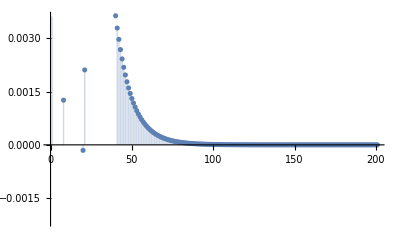

λ=2.  , core={{0.295555,0.626543}}

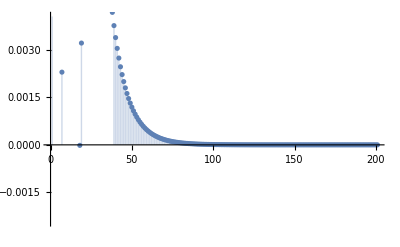

λ=3.  , core={{0.357138,0.80807}}

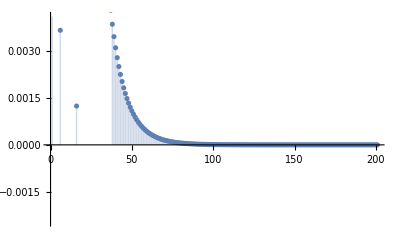

λ=4.  , core={{0.399738,0.942426}}

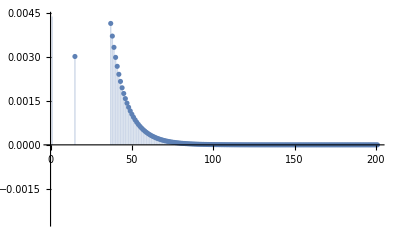

λ=6.  , core={{0.455509,1.12937}}

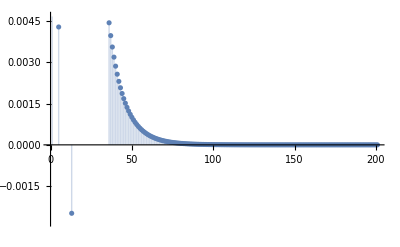

λ=8.  , core={{0.492628,1.2605}}

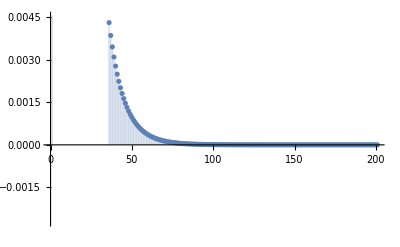

λ=10.  , core={{0.522458,1.36927}}

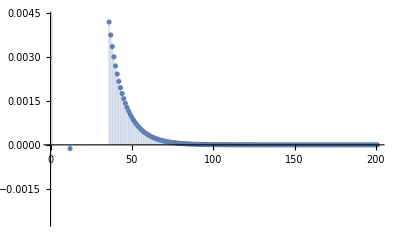

```mathematica
nk=1;

rmip=0.0;
rmap=21;

wfCores={};
wfs={};
w1=1;
amax=10^1;amin=0;
bmin=0.0;bmax=2.1;
w2=Min[Length[#]&/@Mϕ];
Do[
data=Mϕ[[ll]][[w1;;w2]];

modelGauss={Sum[aLn@i Exp[-bLn@i rrel^2],{i,nk}],Table[{amin<aLn@i <amax,bmin<bLn@i <bmax},{i,nk}]};
nlmLABC=NonlinearModelFit[data,modelGauss,Flatten[Table[{{aLn@i,RandomReal[{-0.1,0.1}]},{bLn@i,RandomReal[{0.0001,0.25}]}},{i,nk}],1],rrel,Weights->((#+1)^3&/@data[[All,1]])];
nlresi=nlmLABC["FitResiduals"];
(*modelGauss=Sum[aLn@i Exp[-bLn@i rrel^2],{i,nk}];
nlmLABC=NonlinearModelFit[data,modelGauss,Flatten[Table[{{aLn@i,RandomReal[{-10.1,10.1}]},{bLn@i,RandomReal[{0.0001,0.25}]}},{i,nk}],1],rrel];*)
basispara=Table[{aLn@i,bLn@i},{i,nk}]/.nlmLABC["BestFitParameters"];
AppendTo[wfCores,basispara];
AppendTo[wfs,Normal[nlmLABC]];

Print["λ=",wflambdas[[ll]],"  , core=",wfCores[[-1]]];
GraphicsGrid[{{
Show[ListLogLogPlot[Mϕ[[ll]],PlotLabel->"Λ = "<>ToString[wflambdas[[ll]]]<>" fm^-1"<>"  ;  f_fit=∑_(n = 1)^N c_n·e^(-SubscriptBox[α, n]·SuperscriptBox[ρ, 2]) with N="<>ToString[nk]<>"    Case: "<>ToString[sy]],
LogLogPlot[wfs[[-1]],{rrel,rmip,rmap},PlotLegends->{"original Ψ"},PlotRange->Full, AxesLabel->{"r [fm]","WaveFunction"}],ImageSize->Scaled[.8]],ListPlot[nlresi,Filling->Axis],
Plot[wfs[[-1]],{rrel,rmip,rmap},PlotLegends->{"original Ψ"},PlotRange->Full,Epilog->Map[Point,Mϕ[[ll]]], AxesLabel->{"r [fm]","WaveFunction"},ImageSize->Scaled[.8]]
}},ImageSize->{{1200},{1700}}]//Print
,{ll,Range[Length[wflambdas]]}];
```

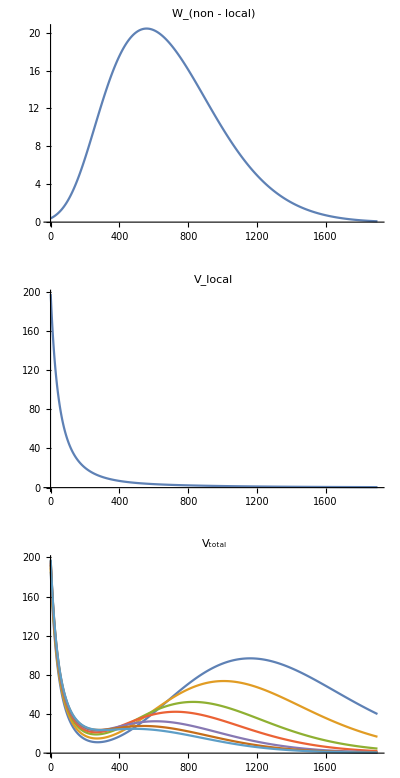

```mathematica
k0FMin=0.002;
k0FMax=0.1;
Divisions=6;
ErangeMeV=N[findLogDivisions[{k0FMin^2/mh2,k0FMax^2/mh2},Divisions]];
pltListloc={};
pltListnonloc={};
pltListFull={};
Lrel=1;
rMax=2;rMin=0.1;dr=0.001;rp=0.01;
Do[
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==wflambdas[[nwf]]&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;
C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
mycore=wfCores[[nwf]];
NM=NormTF[mycore]^2;
eplot=ErangeMeV[[1]];
AppendTo[pltListnonloc,
Chop[Table[NM WnolocTF[rr,rr,ErangeMeV[[2]],λ,C0,D0,mycore[[1]][[2]],mycore[[1]][[2]],Lrel,mh2]
,{rr,rMin,rMax,dr}]]
];
AppendTo[pltListloc,
Chop[Table[(Lrel (Lrel+1)/rr^2)+NM VlocTF[rr,λ,C0,D0,mycore[[1]][[2]],mycore[[1]][[2]](*,Lrel,mh2*)]
,{rr,rMin,rMax,dr}]]
];
AppendTo[pltListFull,
Chop[Table[(Lrel (Lrel+1)/rr^2)+NM VlocTF[rr,λ,C0,D0,mycore[[1]][[2]],mycore[[1]][[2]]]+NM WnolocTF[rr,rr,ErangeMeV[[2]],λ,C0,D0,mycore[[1]][[2]],mycore[[1]][[2]],Lrel,mh2]
,{rr,rMin,rMax,dr}]]
];
,{nwf,Range[Length[wflambdas]]}]

legends="λ = "<>ToString[#]&/@wflambdas;
GraphicsGrid[{{
ListPlot[pltListnonloc[[7]],Joined->True,PlotRange->Full,ImageSize->Large,PlotLabel->"W_(non - local)"]},{
ListPlot[pltListloc[[7]],Joined->True,PlotRange->Full,ImageSize->Large,PlotLabel->"V_local"]},{
ListPlot[pltListFull,Joined->True,PlotRange->Full,ImageSize->Large,PlotLabel->"V_total"]
}}]
Export["/tmp/tmp_VW.dat",Transpose[Prepend[pltListFull,Range[rMin,rMax,dr]]],"Table"];
```

```mathematica
fmin=Table[Select[Differences[pltListFull[[nn]]],#>0&][[1]],{nn,Range[Length[extr]]}]
```

{0.000646896,0.000269138,0.000945708,0.000373031,0.00057528,0.000228995,0.00020441}

```mathematica
Table[Position[Differences[pltListFull[[nn]]],fmin[[nn]]],{nn,Range[Length[extr]]}]
```

{{{274}},{{270}},{{265}},{{263}},{{269}},{{281}},{{303}}}

```mathematica
0.25 wflambdas^2
```

{0.5625,1.,2.25,4.,9.,16.,25.}

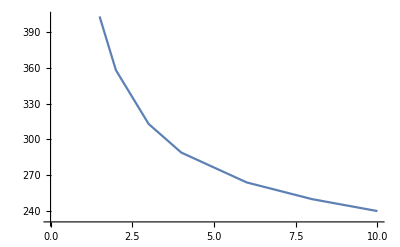

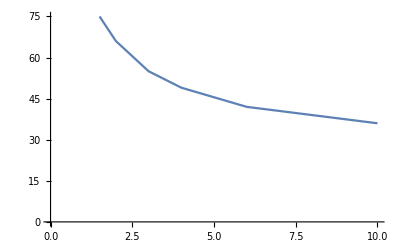

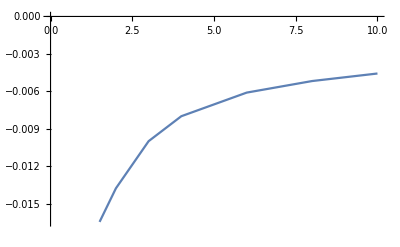

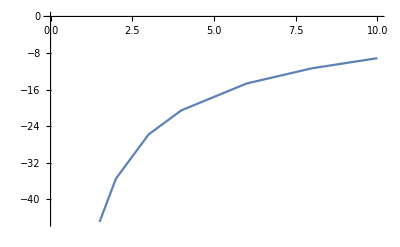

```mathematica
ListPlot[Transpose[{wflambdas,Flatten[Position[#,Min[#]]&/@pltp]}],Joined->True]
ListPlot[Transpose[{wflambdas,Flatten[Position[#,Min[#]]&/@plts]}],Joined->True]
ListPlot[Transpose[{wflambdas,Min[#]&/@pltp}],Joined->True]
ListPlot[Transpose[{wflambdas,Min[#]&/@plts}],Joined->True]
```

```mathematica
vEff[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ,lam_?NumberQ,c0_?NumberQ,d0_?NumberQ,a00_?ArrayQ,TwoMyOverHBsq_?NumberQ]:=Block[{hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,wf,tanDelta,usol,energyMeV,nff,cij},

hDif=Rdis/Npoints;
energyMeV=(momentum^2)/TwoMyOverHBsq;

normsqu=NormTF[a00]^2;

Wmat=ConstantArray[0,{Npoints,Npoints}];

Do[
(*If[a00[[ii]][[1]] a00[[jj]][[1]]≠0,*)

cij=a00[[ii]][[1]] a00[[jj]][[1]] normsqu;

amat=DiagonalMatrix[Table[-hDif^2 TwoMyOverHBsq VlocTF[i hDif,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]]],{i,1,Npoints}]];

wmat=Table[-hDif^3 TwoMyOverHBsq WnolocTF[i hDif,j hDif,energyMeV,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],Lin,TwoMyOverHBsq],{i,1,Npoints},{j,1,Npoints}]; 
(*Print[(Chop[cij (amat+wmat)])[[1;;4,1;;4]]//MatrixForm];*)
Wmat=Wmat+cij (amat+wmat);

(*]*)
,{ii,1,Length[a00]},{jj,1,Length[a00]}];

Dmat=DiagonalMatrix[Table[hDif^2 (-(Lin (Lin+1))/(i hDif)^2),{i,1,Npoints}]];

Amat=Dmat+Wmat;
Amat
]
```

```mathematica
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==wflambdas[[nwf]]&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;
C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
mycore=wfCores[[nwf]];
rMax=5;nGrid=80;
pplot=Sqrt[mh2 ErangeMeV[[1]]];
ve=Chop[vEff[rMax,nGrid,pplot,1,λ,C0,D0,mycore,mh2]];
```

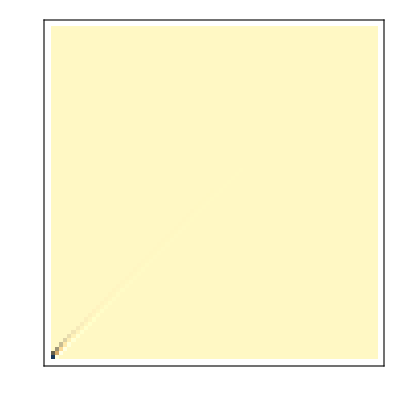

```mathematica
ReliefPlot[ve]
```

```mathematica
ve[[;;5,;;5]]//MatrixForm
```

(-1.9999+3.49497×10^-24 ⅈ | -1.95992×10^-7+5.83338×10^-24 ⅈ | -4.36548×10^-7+3.82753×10^-23 ⅈ | -7.65235×10^-7+8.80287×10^-23 ⅈ | -1.17437×10^-6+5.8628×10^-23 ⅈ
-5.12503×10^-8+1.61049×10^-24 ⅈ | -0.499897+2.30917×10^-23 ⅈ | -4.5379×10^-7+4.94657×10^-23 ⅈ | -7.95376×10^-7+6.03251×10^-23 ⅈ | -1.22046×10^-6+9.2038×10^-23 ⅈ
-5.43967×10^-8+4.6015×10^-24 ⅈ | -2.16243×10^-7+2.33714×10^-23 ⅈ | -0.22212+4.4146×10^-23 ⅈ | -8.4394×10^-7+6.69637×10^-23 ⅈ | -1.29474×10^-6+9.90304×10^-23 ⅈ
-5.85798×10^-8+6.28631×10^-24 ⅈ | -2.32857×10^-7+1.75507×10^-23 ⅈ | -5.18508×10^-7+4.08045×10^-23 ⅈ | -0.124899+7.40627×10^-23 ⅈ | -1.39356×10^-6+1.16391×10^-22 ⅈ
-6.35954×10^-8+3.23485×10^-24 ⅈ | -2.52779×10^-7+1.97249×10^-23 ⅈ | -5.62814×10^-7+4.34204×10^-23 ⅈ | -9.86033×10^-7+8.32233×10^-23 ⅈ | -0.0799002+1.03181×10^-22 ⅈ)